```mathematica
pl=1.0;ph=1.0833;pert=0.5;yv=25;z0=1.6;nz=512;
```

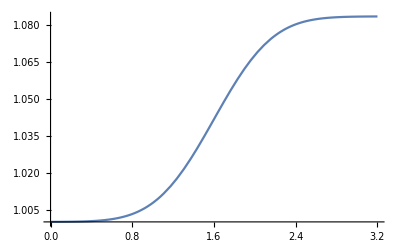

```mathematica
rho[x_,z_]:=0.5(1+Erf[(z-z0)/(10*(z0/yv))+pert*Sin[x]])(ph-pl)+pl;
Plot[rho[Pi,z],{z,0,2*z0}]
```

```mathematica
Show[%84,ImageSize->Tiny]
```

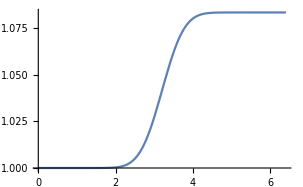

```mathematica
Plot[rho[Pi,z],{z,0,2*z0}]
```

```mathematica
∫(0.5(1+Erf[(z-z0)/(10*(z0/yv))+pert*Sin[x]])(ph-pl)+pl)ⅆz
```

-1.66664+0.000137687 2.71828^(-29127.1 (1.6-1. z-0.00292969 Sin[x])^2)+1.04165 z+Erf[273.067-170.667 z-0.5 Sin[x]] (0.06664-0.04165 z-0.000122021 Sin[x])+0.00305171 Sin[x]

```mathematica
FullSimplify[%87]
```

%87

```mathematica
p[x_,z_]=-1.66664+1.04165 z+Erf[273.0666666666666-170.66666666666663 z-0.5 Sin[x]] (0.06663999999999996-0.04164999999999997 z-0.00012202148437499995 Sin[x])+0.0030517089843750005 Sin[x]
```

-1.66664+1.04165 z+Erf[273.067-170.667 z-0.5 Sin[x]] (0.06664-0.04165 z-0.000122021 Sin[x])+0.00305171 Sin[x]

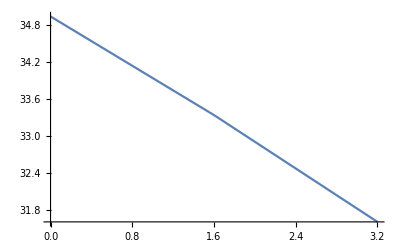

```mathematica
Plot[105-p[Pi,z]-1.66664,{z,0,2*z0}]
```

```mathematica
p[Pi,0]-p[Pi,3.2]
```

-3.33328

```mathematica
∫(0.5(1+Erf[(z-z000)/(5*2*(z000/nzzz))+perttt*Sin[2*x]])(phhh-plll)+plll)ⅆz
```

1/nzzz 0.5 (nzzz (1. phhh z+1. plll z)+2.71828^(-1. (nzzz (-0.1+(0.1 z)/z000)+perttt Sin[2. x])^2) (5.6419 phhh z000-5.6419 plll z000)+Erf[nzzz (-0.1+(0.1 z)/z000)+perttt Sin[2. x]] (nzzz (1. phhh z-1. plll z-1. phhh z000+1. plll z000)+perttt (10. phhh-10. plll) z000 Sin[2. x]))

```mathematica
1/nzzz 0.5 (nzzz (1. phhh z+1. plll z)+2.718281828459045^(-1. (nzzz (-0.1+(0.1 z)/z000)+perttt Sin[x])^2) (5.641895835477563 phhh z000-5.641895835477563 plll z000)+Erf[nzzz (-0.1+(0.1 z)/z000)+perttt Sin[x]] (nzzz (0.9999999999999999 phhh z-0.9999999999999999 plll z-0.9999999999999999 phhh z000+0.9999999999999999 plll z000)+perttt (9.999999999999998 phhh-9.999999999999998 plll) z000 Sin[x]))
1.pl
```

1/nzzz 0.5 (nzzz (1. phhh z+1. plll z)+2.71828^(-1. (nzzz (-0.1+(0.1 z)/z000)+perttt Sin[x])^2) (5.6419 phhh z000-5.6419 plll z000)+Erf[nzzz (-0.1+(0.1 z)/z000)+perttt Sin[x]] (nzzz (1. phhh z-1. plll z-1. phhh z000+1. plll z000)+perttt (10. phhh-10. plll) z000 Sin[x]))

1.

```mathematica
0.8
10.ph
```

0.8

10.833

```mathematica
10.pl
```

10.

```mathematica
rh=1.083; rl=1; g=1; lambda=3.2; a=0.004;re=20000;
vis=ScientificForm[lambda*Sqrt[g*lambda*a/(1+a)]/re]
vis=lambda*Sqrt[g*lambda*a/(1+a)]/re
```

1.80658×10^-5

0.0000180658

```mathematica
"3.61317"×10^("-5")
```

0.0000361317

```mathematica
Rep=lambda*Sqrt[g*lambda*atwood/(1+atwood)]/vis
```

316860. √(atwood/(1+atwood))

```mathematica
ScientificForm[Rep=(lambda √((g lambda atwood)/(1+atwood)))/vis]
```

(3.1686×10^5) √(atwood/(1+atwood))

```mathematica
atwood=0.04; g=1;lambda=3.2;k=2*3.1416926/lambda;
```

```mathematica
vbub=1.025*Sqrt[2*atwood*g/(3*k*(1+atwood))]
```

0.11713

```mathematica
norm=Sqrt[atwood*g*lambda/(1+atwood)]
```

0.350823

```mathematica
vbub/norm
```

0.333873

```mathematica
ScientificForm[Sqrt[2*0.04*(0.4/1024)^3]]
```

2.18366×10^-6

```mathematica
vis=5.61317*10^(-5); ly=3.2; ny=1024;
```

```mathematica
2*0.04*1*(ly/ny)^3/vis^2
```

0.774861

```mathematica
1024*8
```

8192

```mathematica
34.9335-31.6036
```

3.3299